```mathematica
(* This cell contains uninteresting generic setup stuff to prepare for execution of the programs *)

ClearAll["Global`*"];

(* If running from Notebook front end, set directory to Notebook's directory *)
If[Length[$FrontEnd] > 0, NBDir = SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[Length[$FrontEnd] == 0,SetDirectory["/Volumes/Data/Work/BufferStock/BufferStockTheory/Latest/Code/Mathematica/Results/BufferStockTheory"]];

HomeDir = Directory[];
CodeDir = HomeDir<>"/../../CoreCode";
CDToHomeDir := SetDirectory[HomeDir];
CDToCodeDir := SetDirectory[HomeDir<>"/../../CoreCode"];
CDToCodeDir;

<<SetupModelSolutionRoutines.m;
<<SetParamsToBaselineVals.m;
SaveFigs=True;
```

GIC fails (1 < ÞΓ):True

FVAC holds FVA < 1:True

Running FVACnotGICPlot.m

Running cFuncsConvergeSolve.m

Solving for 100 periods.

Constructing TableOfcFuncs.

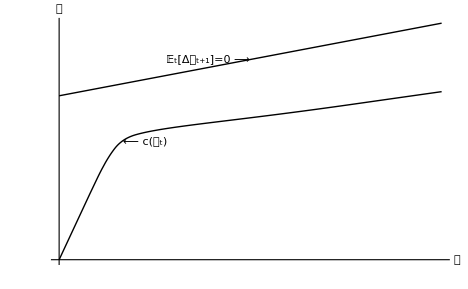

Exporting:../../../../Figures/FVACnotGIC

```mathematica
(* Example of parameters where FVAC holds but GIC fails *)
CDToHomeDir;
<<SetParamsFVACnotGIC.m; 
SetupGrids;
SetupShocks;
Print["GIC fails (1 < ÞΓ):" , 1 < GICValue];
Print["FVAC holds FVA < 1:",FVA < 1];
ConstructLastPeriodToConsumeEverything;
<<FVACnotGICPlot.m;
```

Running cFuncsConvergeSolve.m

Solving for 100 periods.

Constructing TableOfcFuncs.

Running cFuncsConvergePlot.m

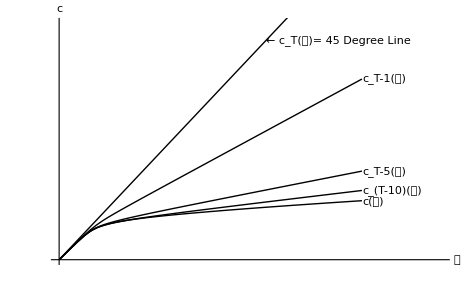

Exporting:../../../../Figures/cFuncsConverge

```mathematica
(* Show convergence of consumption rules iterating back from terminal period T *)
SetParamsBaseline;
SetupGrids;
SetupShocks;
ConstructLastPeriodToConsumeEverything; (* Define terminal consumption rule as the one for the finite horizon *)
CDToHomeDir;
<<cFuncsConvergeSolve.m;
<<cFuncsConvergePlot.m;
```

```mathematica
(* Show characteristics of the converged consumption rule *)
SetParamsBaseline;
ConstructLastPeriod;
aGridVecExcBotSmallLength = 10;
aGridVecExcBotLargeLength = 30;
SetupGrids;
Off[InterpolatingFunction::dmval];
SolveInfHorizToToleranceAtTarget[mTargetDiffAtSuccessiveIterations=0.001];
```

InterpolatingFunction::dmval: Input value {0.106442} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Running cFuncBoundsPlot.m

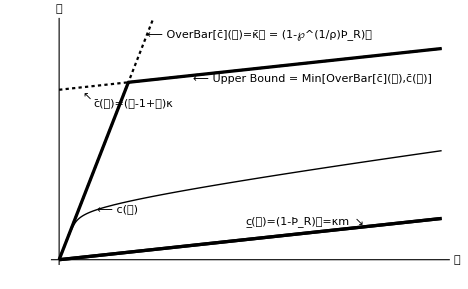

Exporting:../../../../Figures/cFuncBounds

```mathematica
CDToHomeDir;<<cFuncBoundsPlot.m;
```

Running cGroTargetFigPlot.m

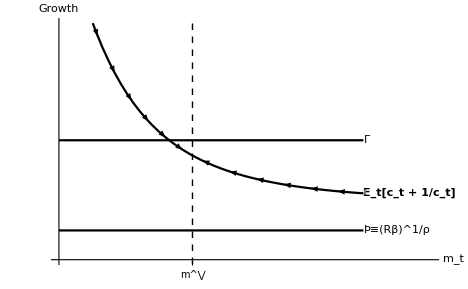

Exporting:../../../../Figures/cGroTargetFig

```mathematica
<<cGroTargetFigPlot.m;
```

Running MPCLimitsPlot.m

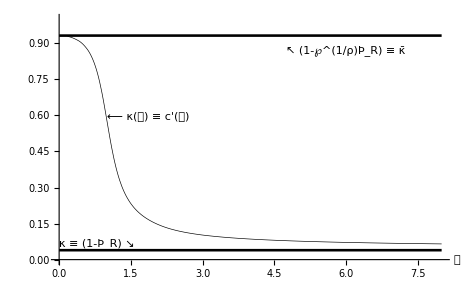

Exporting:../../../../Figures/MPCLimits

```mathematica
<<MPCLimitsPlot.m;
```

Running cRatTargetFigPlot.m

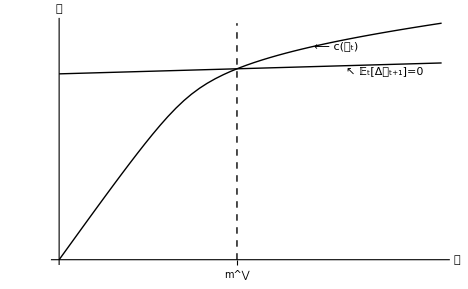

Exporting:../../../../Figures/cRatTargetFig

```mathematica
<<cRatTargetFigPlot.m;
```

```mathematica
<<SimCDFsConverge.m;
```

Running SimCDFsConverge.m

Finished constructing shocks.

Running SimCDFsConvergePlot.m

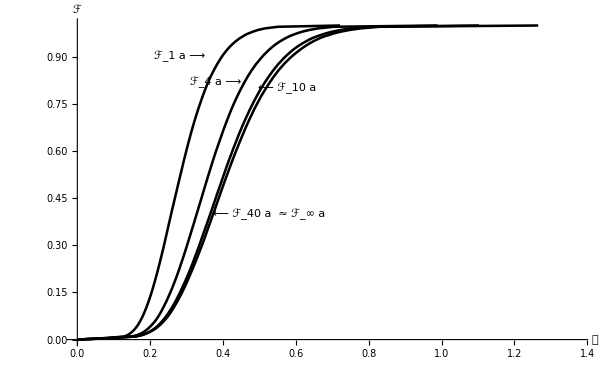

Exporting:../../../../Figures/SimCDFsConverge

```mathematica
<<SimCDFsConvergePlot.m;
```

```mathematica
<<SimRevolution.m;
```

Running SimRevolution.m

$Aborted

Running SimRevolutionPlot.m

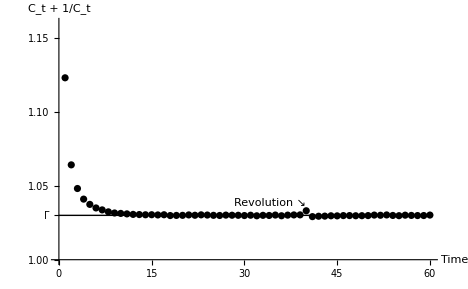

Exporting:../../../../Figures/SimRevolution

```mathematica
<<SimRevolutionPlot.m;
```

{R,β,Γ,ρ}={1.02,0.980392,0.98,2}

PF-GIC fails (Γ < Þ):True

{Γ , Þ=(R)^(1/ρ) β^(1/ρ) , (R)}={0.98,1.,1.02}

Γ <((R) β)^(1/ρ)< R:True

RIC holds (Þ < R):True

⇒ FHWC holds (Γ < R):True

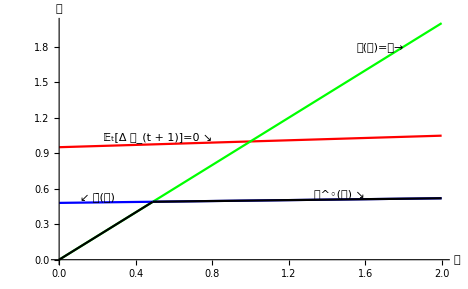

{R,β,Γ,ρ}={1.04,0.980392,1.02,2}

{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}={1.00976,1.02,1.04}

Þ < Γ < R:True

PF-GIC Holds (Þ < Γ):True

RIC holds (Þ < R):True

FHWC holds (Γ < R):True

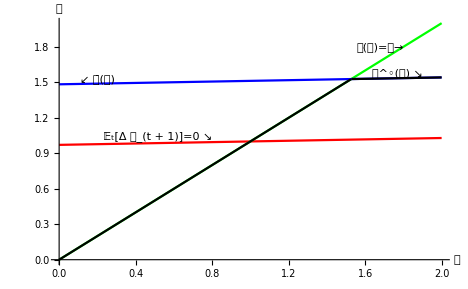

{R,β,Γ,ρ}={1.01,0.97,1.02,2}

Þ=(R)^(1/ρ) β^(1/ρ)=0.989798

PF-GIC holds (Þ < Γ):True

RIC holds (Þ < R):True

FHWC fails (R < Γ):True

PF-FVAC holds Þ/Γ < (R/Γ)^(1/ρ):True

FindRoot::srect: Value Max[1.,If[-101.+𝒷≤0.,1.,(3.97039-1. Log[-101.+𝒷])/Log[ℛ]]] in search specification {nSeek,Max[1,𝓃Approx[𝒷]]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[b♯[nSeek]==𝒷,{nSeek,Max[1,𝓃Approx[𝒷]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value Max[1.,If[-101.+𝒷≤0.,1.,(3.97039-1. Log[-101.+𝒷])/Log[ℛ]]] in search specification {nSeek,Max[1,𝓃Approx[𝒷]]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[b♯[nSeek]==𝒷,{nSeek,Max[1,𝓃Approx[𝒷]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value Max[1.,If[-101.+𝒷≤0.,1.,(3.97039-1. Log[-101.+𝒷])/Log[ℛ]]] in search specification {nSeek,Max[1,𝓃Approx[𝒷]]} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[b♯[nSeek]==𝒷,{nSeek,Max[1,𝓃Approx[𝒷]]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

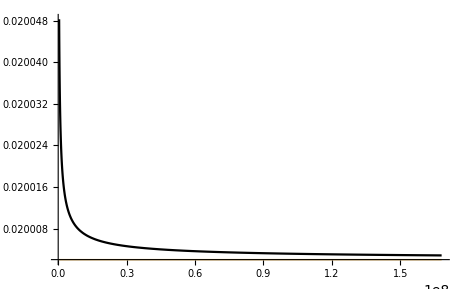

Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC Fails

{R,β,Γ,ρ}={0.98,0.99,1.,2}

{R,β,Γ,ρ}={0.98,1.,0.99,2}

{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}={0.989949,0.99,0.98}

PF-GIC holds (Þ < Γ):True

RIC fails (R < Þ):True

FHWC fails (R < Γ):True

PF-FVAC fails (R/Γ)^(1/ρ) < Þ/Γ (same as 1 < β Γ^(1 - ρ)):True

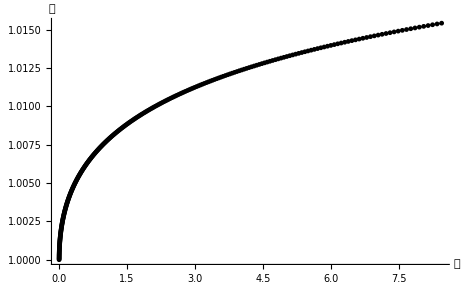

Exporting:../../../../Figures/PFGICHoldsFHWCFailsRICFails

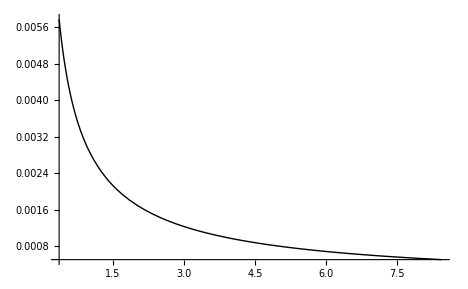

Example where PF-GIC holds, FHWC fails, RIC fails, PF-FVAC holds

{R,β,Γ,ρ}={0.98,0.99,1.,2}

{Þ=(R)^(1/ρ) β^(1/ρ) , Γ , (R)}={0.984987,1.,0.98}

PF-GIC holds (Þ < Γ):True

RIC fails (R < Þ):True

FHWC fails (R < Γ):True

PF-FVAC holds  Þ/Γ < (R/Γ)^(1/ρ)):True

PFGICHoldsFHWCFailsRICPFVACHoldsFails

Exporting:../../../../Figures/PFGICHoldsFHWCFailsRICPFVACHoldsFails

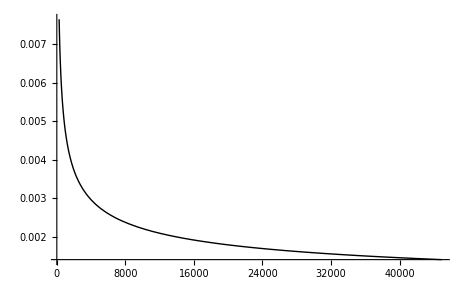

```mathematica
<<doApndxLiqConstr.m;
```

Running doApndxcLim

FindRoot::srect: Value 32.9387 Log[m] in search specification {n,-Log[m]/Log[ÞΓPF]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[m♯[n]==m,{n,-Log[m]/Log[ÞΓPF]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 32.9387 Log[m] in search specification {n,-Log[m]/Log[ÞΓPF]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[m♯[n]==m,{n,-Log[m]/Log[ÞΓPF]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 32.9387 Log[m] in search specification {n,-Log[m]/Log[ÞΓPF]} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[m♯[n]==m,{n,-Log[m]/Log[ÞΓPF]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

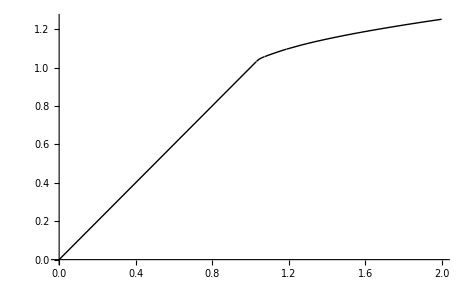

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

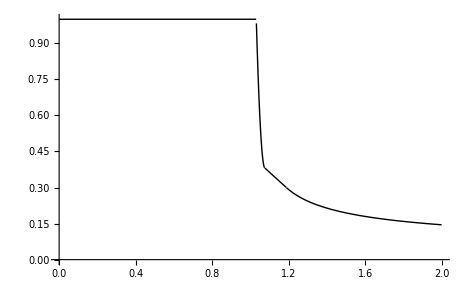

```mathematica
<<doApndxcLim.m;
```